### Naloga 1

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

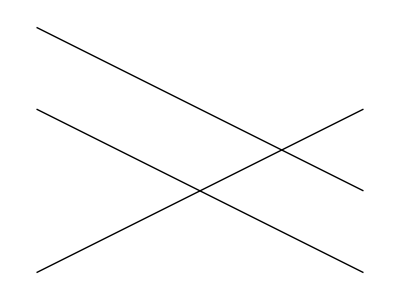

```mathematica
Narisi[d, d2,d3]
```

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

### Naloga 2

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

Naloga 3

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{{0,0},{1,1},{0,3},{-1,2},First[m1]}]
```

```mathematica
?Slika
```

Global`Slika

Slika[Mnogokotnik[t__]]:=Line[{{0,0},{1,1},{0,3},{-1,2},First[m1]}]

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

```mathematica
Narisi[m__Mnogokotnik]:=Graphics[Slika[m1]]
```

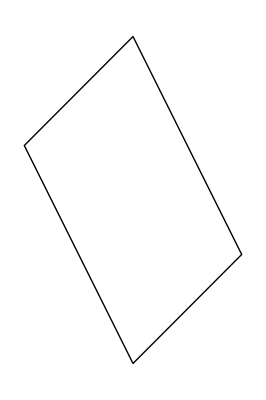

```mathematica
Narisi[m1]
```

```mathematica
ClearAll[PravilniNKotnik]
```

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[{Table[{r* Cos[(2*Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]}],Point[ {0,0}]}]
?PravilniNKotnik
```

Global`PravilniNKotnik

PravilniNKotnik[n_,r_]:=Graphics[{Line[{Table[{r Cos[(2 π i)/n],r Sin[(2 π i)/n]},{i,0,n}]}],Point[{0,0}]}]

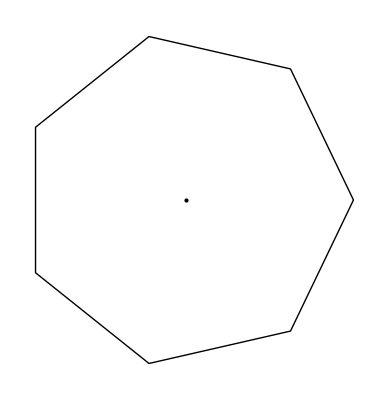

```mathematica
p5=PravilniNKotnik[7,2]
```

```mathematica
PravilniNKotnik[n_,r_,phi_]:=Manipulate[Graphics[{Line[{Table[{r* Cos[(2*Pi * i+phi)/n],r*Sin[(2 Pi *i+phi)/n]},{i,0,n}]}],Point[ {0,0}]}]
,{phi,2,20}]
```

```mathematica
PravilniNKotnik[10,3,phi]
```

4. Naloga

5. Naloga